```mathematica
Clear[montecarlo];
montecarlo[n_,f_,xmin_,xmax_,ymax_] :=
Block[{boxarea=ymax*(xmax-xmin),
nymax=N[ymax],
nxmax=N[xmax],
nxmin=N[xmin],
count=0,
randpoint,
pointlist={}
},
For[i=1,i≤n,i++,
randpoint={Random[Real,{nxmin,nxmax}],
Random[Real,{0,nymax}]
};
pointlist=Append[pointlist,randpoint];
If[(randpoint[[2]]≤f[randpoint[[1]]]),
count++
];
];
Print[(count/n)*ymax*(xmax-xmin)//N];

Show[{Plot[f[x],{x,xmin,xmax},
DisplayFunction->Identity],
ListPlot[pointlist,DisplayFunction->Identity]
},DisplayFunction->$DisplayFunction,
AspectRatio->1
]
]
```

```mathematica
Clear[f];
f[x_]:=x^2
```

0.38

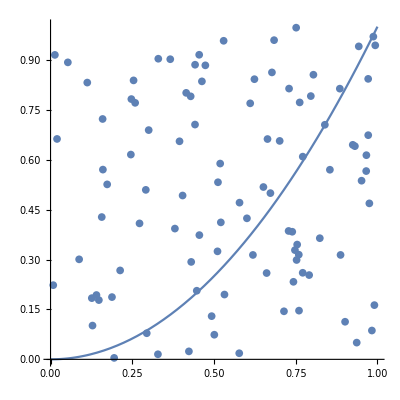

```mathematica
montecarlo[100,f,0,1,1]
```

0.958186

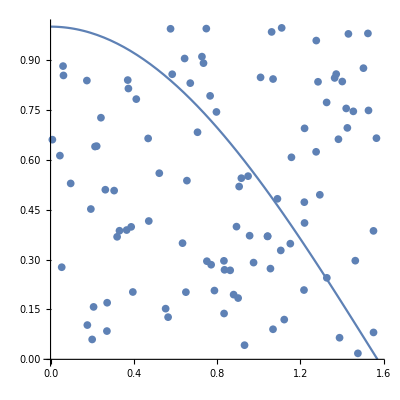

```mathematica
montecarlo[100,Cos,0,Pi/2,1]
```

```mathematica
<<ComputationalGeometry`
```

ConvexHull::shdw: Symbol "ConvexHull" appears in multiple contexts {"ComputationalGeometry`", "Global`"}; definitions in context "ComputationalGeometry`" may shadow or be shadowed by other definitions.

```mathematica
Clear[montecarlo];

circlep[x_]:={x,1/2+Sqrt[x-x^2]}
circlem[x_]:={x,1/2-Sqrt[x-x^2]}
pcircle=Join[Map[circlep,Range[0,1,.001]],Map[circlem,Range[0,1,.001]]];
montecarlo=Block[{randpoint,
count =0},
For[i=0,i≤1000,i++,
randpoint={RandomReal[Real,{0,1}],
RandomReal[Real,{0,1}]};
If [randpoint[[2]<circlep[1/2]&&randpoint[[2]]>circlem[1/2],
count++
];
];
Print[(count/1000)//N];
]
```

1.001

```mathematica
inPolyQ[pcircle,{1,1}]
```

True

```mathematica
Solve[(x-1/2)^2+(y-1/2)^2-1/4==0,y,Reals]
```

{{y→ConditionalExpression[1/2-√(x-x^2),0<x<1]},{y→ConditionalExpression[1/2+√(x-x^2),0<x<1]}}

```mathematica
Plot[pcircle,{x,0,1}]
```

Plot::pllim: Range specification {0, 1} is not of the form {x, xmin, xmax}.

Plot[pcircle,{0,1}]